{{29.3842,177.941},{30.6421,187.779},{0,190},{0,180},{30.0802,182.869},{15.4185,189.446},{0,185},{14.8044,179.487}}

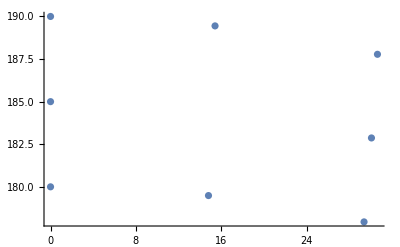

```mathematica
pl={{29.384208, 177.941476},{30.6420516, 187.778966},{0, 190 },{0 ,180 },{30.0801769, 182.868838},{15.4185372, 189.445695 },{0 ,185 },{14.8043826, 179.4869889 }}
ListPlot[Labeled[pl]]
```

```mathematica
320 326 339 336 323 334 338 330
```

```mathematica
326 332 341 339 329 337 340 334
```

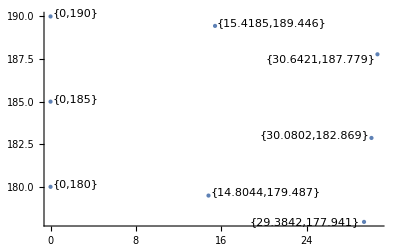

```mathematica
ListPlot[Labeled[#,#]&/@pl,PlotStyle->PointSize[Medium]]
```

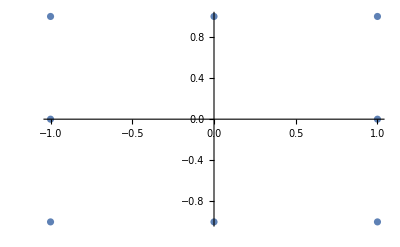

```mathematica
ListPlot[{{1,-1},{1,1},{-1,1},{-1,-1},{1,0},{0,1},{-1,0},{0,-1}}]
```

```mathematica
c={{sx,0.,0.},{0.,0.,0.},{0.,0.,0.}}
s=c-0.6667 Tr[c]IdentityMatrix[3]
js=0.5Sqrt[s.s];
data=Expand[Sqrt[3 js]]
```

{{sx,0.,0.},{0.,0.,0.},{0.,0.,0.}}

{{sx-0.6667 (0.+sx),0.,0.},{0.,0.-0.6667 (0.+sx),0.},{0.,0.,0.-0.6667 (0.+sx)}}

{{0.707071 (sx^2)^(1/4),0.,0.},{0.,1.00002 (sx^2)^(1/4),0.},{0.,0.,1.00002 (sx^2)^(1/4)}}

```mathematica
data//N
```

{{0.707071 (sx^2)^(1/4),0.,0.},{0.,1.00002 (sx^2)^(1/4),0.},{0.,0.,1.00002 (sx^2)^(1/4)}}

```mathematica
0.70707142496356(sx^2.)^(1/4.)
```

0.707071 (sx^2.)^0.25

```mathematica
0.70707142496356 sx^0.5
```

0.707071 sx^0.5

```mathematica
D[(0.70707142496356 sx^0.5), sx]
```

0.353536/sx^0.5

```mathematica
1577-1237
```

340

```mathematica
p={{15.64344650, 98.76883410},
{16.28828790, 108.52753600},
{0.00000000, 110.00000000},
{0.00000000 ,100.00000000},
{15.87966380 ,103.63710600},
{8.11919151, 109.62950500},
{0.00000000 ,105.00000000},
{7.84590957 ,99.69173340}}
```

{{15.6434,98.7688},{16.2883,108.528},{0.,110.},{0.,100.},{15.8797,103.637},{8.11919,109.63},{0.,105.},{7.84591,99.6917}}

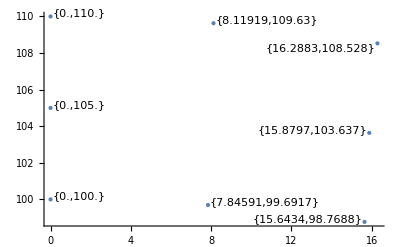

```mathematica
ListPlot[Labeled[#,#]&/@p,PlotStyle->PointSize[Medium]]
```

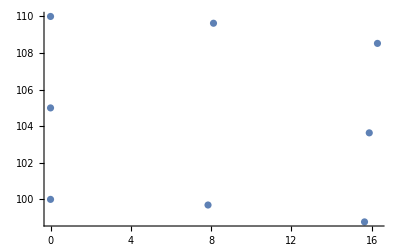

```mathematica
ListPlot[p]
```

```mathematica
1235-895
```

340